{3.1144+33.1644/x, | Estimate | Standard Error | t-Statistic | P-Value
a | 33.1644 | 5.97583 | 5.54977 | 0.0309674
b | 3.1144 | 0.198968 | 15.6528 | 0.00405664}

{5.63251+40.6655/(√x), | Estimate | Standard Error | t-Statistic | P-Value
a | 40.6655 | 4.13079 | 9.84448 | 0.0101614
b | 5.63251 | 0.694737 | 8.1074 | 0.0148752}

{21924.3 ⅇ^(-107.068/(506-x)-1500/(-293+x)), | Estimate | Standard Error | t-Statistic | P-Value
a | 21924.3 | 36395.7 | 0.602386 | 0.654842
b | 107.068 | 65.5141 | 1.63427 | 0.34958
c | 1. | 0. | ∞ | 0.}

{21924.3 ⅇ^(-107.068/(506-x)-1500/(-293+x))}

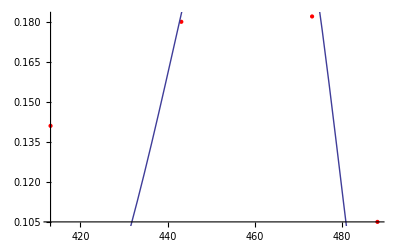

```mathematica
Clear[a, x, b, data, fit];
data = {{17.85,4.89},{32.85,4.28},{62.85,3.77}, {92.85,3.27}};
fit = NonlinearModelFit[data,a / x + b,{a, b},{x}];
fit[{"BestFit","ParameterTable"}]

Clear[a, x, b, data, fit];
data = {{17.85,15},{32.85,13.2},{62.85,10.8}, {92.85,9.6}};
fit = NonlinearModelFit[data,a / Sqrt[x] + b,{a, b},{x}];
fit[{"BestFit","ParameterTable"}]

Clear[a, x, b, c, data, fit];
data = {{140 + 273.15,0.141},{170+ 273.15,0.180},{200+273.15,0.182}, {215+273.15,0.105}};

fit = NonlinearModelFit[data,a*Exp[-c/(x-(343-50))]*Exp[-b/(506-x)],{a, b, c},{x}];
fit[{"BestFit","ParameterTable"}]
Text[fit[{"BestFit"}]]

Show[ListPlot[data,PlotStyle->Red],Plot[{fit["BestFit"]},{x,420,500}]]
```

```mathematica
{5176.318963421481 ⅇ^(-63.31265549115383/(506-x)-1500/(-294+x)),{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {a, 5176.318963421481, 10233.399315118822, 0.5058259532366717, 0.7018725508919965}, {b, 63.31265549115383, 61.01281304898557, 1.0376944174057632, 0.48822479241652195}, {c, 1., 0., ∞, 0``307.6526555685888}}}
```

\left\{5176.32 e^{-\frac{1500}{x-294}-\frac{63.3127}{506-x}}\right\}